# Elementary Intro

## 7. Colors and Styles

```mathematica
Grid[Table[Style[i+j,RandomColor[]],{i,10},{j,10}]]
```

```mathematica
{{2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {3, 4, 5, 6, 7, 8, 9, 10, 11, 12}, {4, 5, 6, 7, 8, 9, 10, 11, 12, 13}, {5, 6, 7, 8, 9, 10, 11, 12, 13, 14}, {6, 7, 8, 9, 10, 11, 12, 13, 14, 15}, {7, 8, 9, 10, 11, 12, 13, 14, 15, 16}, {8, 9, 10, 11, 12, 13, 14, 15, 16, 17}, {9, 10, 11, 12, 13, 14, 15, 16, 17, 18}, {10, 11, 12, 13, 14, 15, 16, 17, 18, 19}, {11, 12, 13, 14, 15, 16, 17, 18, 19, 20}}
```

## 8. Basic Graphics Objects

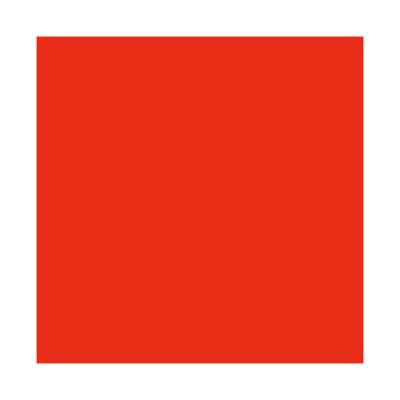
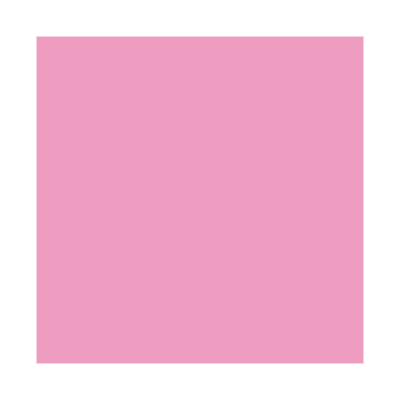
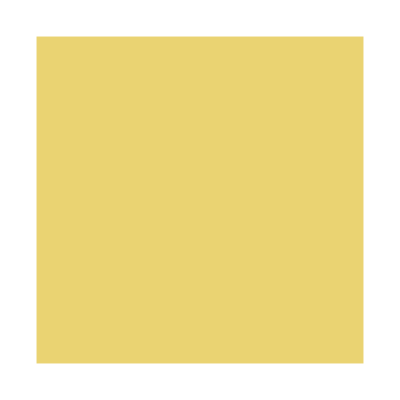
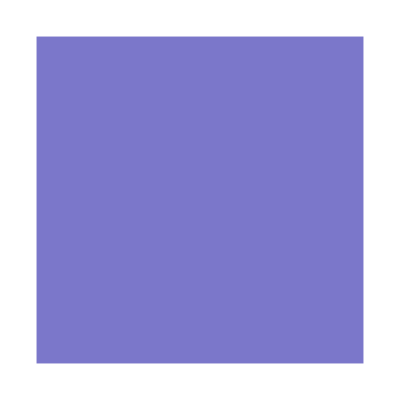
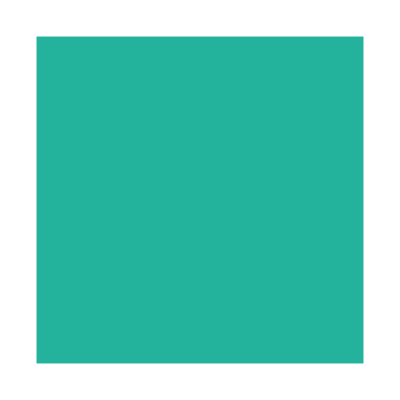

```mathematica
Row[Table[Graphics[{RandomColor[], Rectangle[]}],5]]
```

## 9. Interactive Manipulation

```mathematica
Manipulate[Graphics[
Style[RegularPolygon[n],RGBColor[{r,g,b,a}]]],
{n,3,10,1},{r,0,1},{g,0,1},{b,0,1},{{a,1},0,1}]
```

## 10. Images

```mathematica
Image[EntityValue[LinguisticAssistant,"Image"],ImageSize->Medium]//EdgeDetect
```

-Graphics-

## 11. Strings and Text

```mathematica
WikipediaData["c. elegans"]//WordCloud//Rasterize//ColorNegate
```

-Graphics-

## 12. Sound

```mathematica
Sound[Table[SoundNote[RandomChoice[Characters["ACDEG"]]],5]]
```

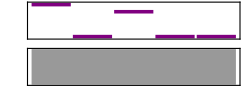

Note: doesn’t play sound :DDDDDDD

## 13. Arrays

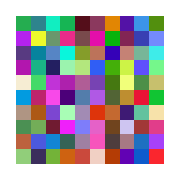

```mathematica
ArrayPlot[Table[RandomColor[],10,10], ImageSize->Small]
```

## 14. Coordinates and Graphics

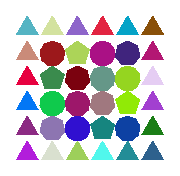

```mathematica
Graphics[Table[Style[RegularPolygon[{x,y},1,3+Mod[x*y,10]],RandomColor[]],{x,0,10,2},{y,0,10,2}], ImageSize->Small]
```

## 15. Scope of the Wolfram Language

```mathematica
Take[WolframLanguageData[],10]
```

{$Aborted,$ActivationKey,$AllowDataUpdates,$AllowExternalChannelFunctions,$AllowInternet,$AssertFunction,$Assumptions,$AudioDecoders,$AudioEncoders,$AudioInputDevices}

```mathematica
Select[Take[WolframLanguageData[],100],StringContainsQ[EntityValue[#,"Name"],"Audio"]&]
```

{$AudioDecoders,$AudioEncoders,$AudioInputDevices,$AudioOutputDevices,$DefaultAudioInputDevice,$DefaultAudioOutputDevice}

```mathematica
$UserBaseDirectory
```

/home/ben/.Mathematica

## 16. Real-World Data

```mathematica
EntityProperties[Entity["MusicAct","ChristianMcBride::fq792"]]
```

{albums,country,end date,image,members,members and dates,name,place of origin,start date,works}

```mathematica
Entity["MusicAct","ChristianMcBride::fq792"]["Albums"]
```

{Parker's Mood,Gettin' to It,Number Two Express,SuperBass,Fingerpainting: The Music of Herbie Hancock,A Family Affair,SuperBass 2,Live at Tonic,New York Time,Super Trio,Camp Meeting,Tokyo Day Trip Live,Day Trip,Best of New York Sessions, Volume Two,Conversations With Christian,My Witch's Blue,Christian McBride’s New Jawn,Trilogy 2,The Movement Revisited: A Musical Portrait of Four Icons,RoundAgain,Sci-Fi,Vertical Vision}

```mathematica
Entity["MusicAlbum","Trilogy2::45z72"]["CanonicalMusicWorkRecordings"]
```

{How Deep Is the Ocean (Trilogy 2, Live),500 Miles High (Trilogy 2, Live),Crepuscule with Nellie (Trilogy 2, Live),Work (Trilogy 2, Live),But Beautiful (Trilogy 2, Live),La Fiesta (Trilogy 2, Live),Eiderdown (Trilogy 2, Live),All Blues (Trilogy 2, Live),Pastime Paradise (Trilogy 2, Live),Now He Sings, Now He Sobs (Trilogy 2, Live),Serenity (Trilogy 2, Live),Lotus Blossom (Trilogy 2, Live)}

## 17. Units

```mathematica
InputForm[EntityInstance[Entity["Element","Carbon"], Quantity[1, "Kilograms"]]]
```

EntityInstance[Entity["Element", "Carbon"], Quantity[1, "Kilograms"]]

```mathematica
UnitConvert[EntityValue[EntityList[EntityClass["Planet",All]],"DistanceFromEarth"],Quantity[, "LightMinutes"]]
```

{11.091 light minutes,14.2961 light minutes,0. light minutes,15.5263 light minutes,45.9674 light minutes,85.2706 light minutes,172.305 light minutes,255.966 light minutes}

## 18. Geocomputation

```mathematica
GeoDistance[Entity["AdministrativeDivision",{"Maryland","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}]]
```

2180.77 mi

```mathematica
GeoGraphics[Entity["AdministrativeDivision",{"Maryland","UnitedStates"}]]
```

-Graphics-

```mathematica
GeoGraphics[GeoPath[{Entity["AdministrativeDivision",{"Maryland","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}]}]]
```

-Graphics-

## 19. Dates and Times

```mathematica
Now
```

Mon 12 Apr 2021 15:55:34GMT-4

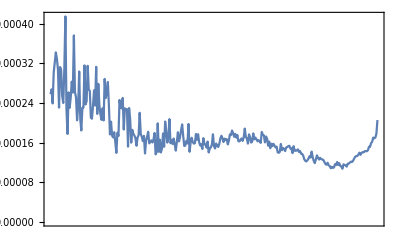

```mathematica
DateListPlot[WordFrequencyData["think","TimeSeries"]]
```

```mathematica
DateObject[{2021, 6, 28}]-Now
```

76. days

## 20. Options

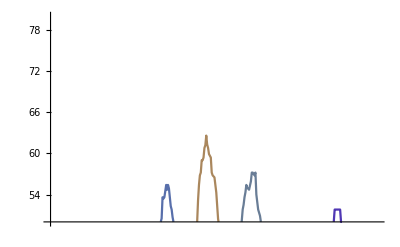

```mathematica
DateListPlot[
AirTemperatureData[Entity["City",{"Paris","IleDeFrance","France"}],{DatePlus[Today, -Quantity[1, "Weeks"]], Now}], 
PlotRange->{50,80},Frame->False,ColorFunction->"Rainbow"]
```

## 21. Graphs and Networks

```mathematica
Manipulate[Graph[
Flatten[Table[i->j,{i,m},{j,m}]],VertexLabels->"Name"],
{m,1,10,1}]
```

## 22. Machine Learning

```mathematica
Classify["Sentiment",{"I don't like","I like everything", "I don't hate"}]
```

{Negative,Positive,Negative}

{RGBColor[0.8535642814574338, 0.15772466147397712, 0.8580196841854286],RGBColor[0.3443486080006981, 0.6422751001373053, 0.3360733638569886],RGBColor[0.3541926425397739, 0.2959611559659039, 0.9559830896868329],RGBColor[0.08551083691438421, 0.6888746025398258, 0.2239826140490866],RGBColor[0.9404816975363262, 0.08545272251318137, 0.9223338849585192],RGBColor[0.2268596034228303, 0.11716717237446628, 0.3127299616437369],RGBColor[0.6264411372209426, 0.6186228130246765, 0.8507188915090753],RGBColor[0.7933200172738919, 0.39303139910037577, 0.9381684236762917],RGBColor[0.9879751467738862, 0.7514040058019009, 0.9708653011732282],RGBColor[0.7095910255834188, 0.9332671972874065, 0.052705022852911565],RGBColor[0.7478828933410211, 0.44673253658167345, 0.24909747343703992],RGBColor[0.25284091191360947, 0.2298353231965553, 0.559911538749265],RGBColor[0.5964905252213699, 0.7854232882746985, 0.0005451295928871058],RGBColor[0.42612007175330335, 0.4238572966582932, 0.10332777214184685],RGBColor[0.8394027049148882, 0.1169867376132907, 0.9014114466742487],RGBColor[0.6812925581818767, 0.23434002751010174, 0.6217439310077824],RGBColor[0.8095080361074045, 0.5289308656879794, 0.9111074876326664],RGBColor[0.32764036213456627, 0.45708545593282546, 0.4095544481672089],RGBColor[0.15498838166329398, 0.15824303986515353, 0.6587804604002669],RGBColor[0.22621905918162577, 0.7193803548125817, 0.8898197336276237],RGBColor[0.9844545455992038, 0.21242091139682073, 0.32876434328478354],RGBColor[0.18189876666664495, 0.6385491259797123, 0.8368047767887115],RGBColor[0.9689516735485106, 0.5397094435471064, 0.05824677614062379],RGBColor[0.9997598351509964, 0.07342083465184124, 0.31382379879394295],RGBColor[0.07750063518124528, 0.4811878406264323, 0.15957682423803132],RGBColor[0.23229534277969988, 0.5887634302236586, 0.47684284435185975],RGBColor[0.6500256230166142, 0.10453193228666158, 0.766119230916841],RGBColor[0.7649309990830877, 0.23030815895749646, 0.45594811158433735],RGBColor[0.3313846686731188, 0.5533027603000169, 0.8071226293648672],RGBColor[0.5502576047959316, 0.9988156952478551, 0.05519909326499395],RGBColor[0.46324223754918603, 0.28333107783830846, 0.019442654729932896],RGBColor[0.479976372433194, 0.31835727234355793, 0.9145904192418854],RGBColor[0.24622976506336514, 0.707332548074562, 0.307702099741453],RGBColor[0.07133340166769853, 0.8921894169406794, 0.25419007044048136],RGBColor[0.3983036668984483, 0.783425564455486, 0.07443094528765726],RGBColor[0.6351720848321258, 0.4344672721539702, 0.38199763768169825],RGBColor[0.7837045730705259, 0.2426188682642374, 0.4922797496712161],RGBColor[0.4856280933303625, 0.19208654604975073, 0.013481533280932156],RGBColor[0.026464853508305408, 0.5987346259033808, 0.7543774310939013],RGBColor[0.7763492152028821, 0.8245392738689727, 0.36960159759456346],RGBColor[0.5329967170451344, 0.5492791360986118, 0.8296542522115218],RGBColor[0.5701426197874235, 0.902368845343235, 0.6954682879776131],RGBColor[0.7463659418304378, 0.0065179010570348694, 0.14826369583755739],RGBColor[0.526636095568116, 0.29981549021175025, 0.7426698353846952],RGBColor[0.45180103939396643, 0.5584025461085773, 0.3608651056100971],RGBColor[0.5436824608711355, 0.6368265562729978, 0.20859778953467956],RGBColor[0.12107063893629055, 0.5916075095543469, 0.30365612533873554],RGBColor[0.7354306350293238, 0.7706832421579728, 0.010092174004172616],RGBColor[0.3613279246594756, 0.9559056100621954, 0.7523500136612113],RGBColor[0.022680497248779963, 0.7099025878591139, 0.6062844254021029]}

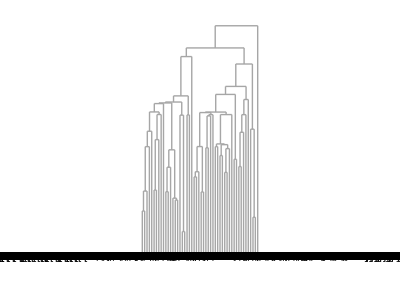

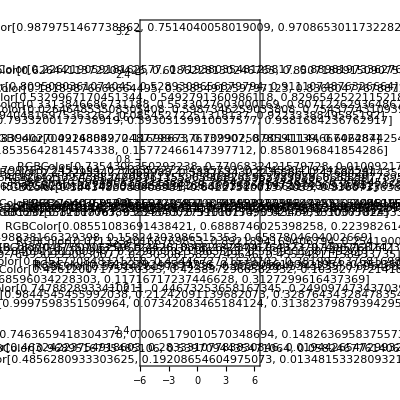

RGBColor[0.8535642814574338, 0.15772466147397712, 0.8580196841854286]RGBColor[0.3541926425397739, 0.2959611559659039, 0.9559830896868329]RGBColor[0.9404816975363262, 0.08545272251318137, 0.9223338849585192]RGBColor[0.2268596034228303, 0.11716717237446628, 0.3127299616437369]RGBColor[0.7933200172738919, 0.39303139910037577, 0.9381684236762917]RGBColor[0.25284091191360947, 0.2298353231965553, 0.559911538749265]RGBColor[0.8394027049148882, 0.1169867376132907, 0.9014114466742487]RGBColor[0.6812925581818767, 0.23434002751010174, 0.6217439310077824]RGBColor[0.15498838166329398, 0.15824303986515353, 0.6587804604002669]RGBColor[0.6500256230166142, 0.10453193228666158, 0.766119230916841]RGBColor[0.7649309990830877, 0.23030815895749646, 0.45594811158433735]RGBColor[0.479976372433194, 0.31835727234355793, 0.9145904192418854]RGBColor[0.7837045730705259, 0.2426188682642374, 0.4922797496712161]RGBColor[0.5329967170451344, 0.5492791360986118, 0.8296542522115218]RGBColor[0.526636095568116, 0.29981549021175025, 0.7426698353846952]
RGBColor[0.3443486080006981, 0.6422751001373053, 0.3360733638569886]RGBColor[0.08551083691438421, 0.6888746025398258, 0.2239826140490866]RGBColor[0.7095910255834188, 0.9332671972874065, 0.052705022852911565]RGBColor[0.7478828933410211, 0.44673253658167345, 0.24909747343703992]RGBColor[0.5964905252213699, 0.7854232882746985, 0.0005451295928871058]RGBColor[0.42612007175330335, 0.4238572966582932, 0.10332777214184685]RGBColor[0.32764036213456627, 0.45708545593282546, 0.4095544481672089]RGBColor[0.9689516735485106, 0.5397094435471064, 0.05824677614062379]RGBColor[0.07750063518124528, 0.4811878406264323, 0.15957682423803132]RGBColor[0.23229534277969988, 0.5887634302236586, 0.47684284435185975]RGBColor[0.5502576047959316, 0.9988156952478551, 0.05519909326499395]RGBColor[0.46324223754918603, 0.28333107783830846, 0.019442654729932896]RGBColor[0.24622976506336514, 0.707332548074562, 0.307702099741453]RGBColor[0.07133340166769853, 0.8921894169406794, 0.25419007044048136]RGBColor[0.3983036668984483, 0.783425564455486, 0.07443094528765726]RGBColor[0.6351720848321258, 0.4344672721539702, 0.38199763768169825]RGBColor[0.4856280933303625, 0.19208654604975073, 0.013481533280932156]RGBColor[0.7763492152028821, 0.8245392738689727, 0.36960159759456346]RGBColor[0.5701426197874235, 0.902368845343235, 0.6954682879776131]RGBColor[0.45180103939396643, 0.5584025461085773, 0.3608651056100971]RGBColor[0.5436824608711355, 0.6368265562729978, 0.20859778953467956]RGBColor[0.12107063893629055, 0.5916075095543469, 0.30365612533873554]RGBColor[0.7354306350293238, 0.7706832421579728, 0.010092174004172616]RGBColor[0.3613279246594756, 0.9559056100621954, 0.7523500136612113]RGBColor[0.022680497248779963, 0.7099025878591139, 0.6062844254021029]
RGBColor[0.6264411372209426, 0.6186228130246765, 0.8507188915090753]RGBColor[0.9879751467738862, 0.7514040058019009, 0.9708653011732282]RGBColor[0.8095080361074045, 0.5289308656879794, 0.9111074876326664]RGBColor[0.22621905918162577, 0.7193803548125817, 0.8898197336276237]RGBColor[0.18189876666664495, 0.6385491259797123, 0.8368047767887115]RGBColor[0.3313846686731188, 0.5533027603000169, 0.8071226293648672]RGBColor[0.026464853508305408, 0.5987346259033808, 0.7543774310939013]
RGBColor[0.9844545455992038, 0.21242091139682073, 0.32876434328478354]RGBColor[0.9997598351509964, 0.07342083465184124, 0.31382379879394295]RGBColor[0.7463659418304378, 0.0065179010570348694, 0.14826369583755739]

```mathematica
colors=Table[RandomColor[],50]
Dendrogram[colors]
FeatureSpacePlot[colors,Frame->True]
Column[Row/@FindClusters[colors]]
```

## 23. More About Numbers

```mathematica
N[Pi,50]-Round[Pi]
```

0.141592653589793238462643383279502884197169399375

## 24. More Forms of Visualization

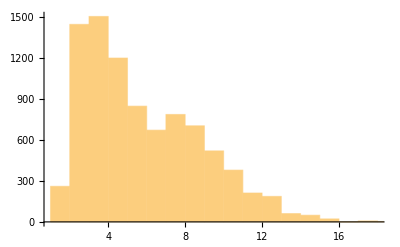

```mathematica
Histogram[StringLength/@TextWords[WikipediaData["computers"]]]
```

## 25. Ways to Apply Functions

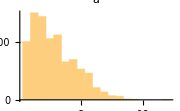
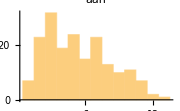
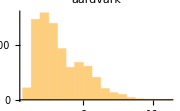

```mathematica
Histogram[StringLength/@TextWords[WikipediaData[#]],PlotLabel->#,ImageSize->Small]&/@Take[WordList[],3]//Row
```

## 26. Pure Anonymous Functions

```mathematica
(#^2+1&)/@Range[10]
```

{2,5,10,17,26,37,50,65,82,101}

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

## 27. Applying Functions Repeatedly

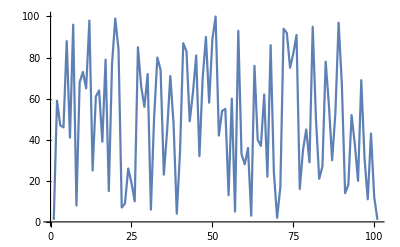

```mathematica
NestList[Mod[59#,101]&,1,100]//ListLinePlot
```

## 28. Tests and Conditionals

```mathematica
Select[Range[25],Mod[#,10]==3&]
```

{3,13,23}

```mathematica
Table[If[i==j,1,0],{i,5},{j,5}]//Grid
```

1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1

## 29. More about Pure Functions

```mathematica
Array[Prime,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
FoldList[(#1*#2)&,1,Array[Prime,10]]
```

{1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

```mathematica
Array[If[#1>=#2,1,0]&,{10,10}]//Grid
```

1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1

## 30. Rearranging Lists

```mathematica
Thread[Alphabet[]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
Select[Table[StringJoin[Table[RandomChoice[Alphabet[]],4]],1000],MemberQ[WordList[],#]&]
```

{rung,haft,skin,fang,burg}

## 31. Parts of Lists

```mathematica
TakeLargestBy[WordList[],StringLength,10]
```

{electroencephalographic,electroencephalograph,counterrevolutionary,buckminsterfullerene,compartmentalization,electroencephalogram,internationalization,uncharacteristically,magnetohydrodynamics,incomprehensibility}

## 32. Patterns

```mathematica
Cases[IntegerDigits[Range[1000]],{1,_,9}]
```

{{1,0,9},{1,1,9},{1,2,9},{1,3,9},{1,4,9},{1,5,9},{1,6,9},{1,7,9},{1,8,9},{1,9,9}}

```mathematica
Cases[IntegerDigits[Range[1000]],{x_,x_,x_}]
```

{{1,1,1},{2,2,2},{3,3,3},{4,4,4},{5,5,5},{6,6,6},{7,7,7},{8,8,8},{9,9,9}}

```mathematica
IntegerDigits[Range[100]]/.{0->Gray,9->Orange}
```

{{1},{2},{3},{4},{5},{6},{7},{8},{RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5]},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,RGBColor[1, 0.5, 0]},{2,GrayLevel[0.5]},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,RGBColor[1, 0.5, 0]},{3,GrayLevel[0.5]},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,RGBColor[1, 0.5, 0]},{4,GrayLevel[0.5]},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,RGBColor[1, 0.5, 0]},{5,GrayLevel[0.5]},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,RGBColor[1, 0.5, 0]},{6,GrayLevel[0.5]},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,RGBColor[1, 0.5, 0]},{7,GrayLevel[0.5]},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,RGBColor[1, 0.5, 0]},{8,GrayLevel[0.5]},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,RGBColor[1, 0.5, 0]},{RGBColor[1, 0.5, 0],GrayLevel[0.5]},{RGBColor[1, 0.5, 0],1},{RGBColor[1, 0.5, 0],2},{RGBColor[1, 0.5, 0],3},{RGBColor[1, 0.5, 0],4},{RGBColor[1, 0.5, 0],5},{RGBColor[1, 0.5, 0],6},{RGBColor[1, 0.5, 0],7},{RGBColor[1, 0.5, 0],8},{RGBColor[1, 0.5, 0],RGBColor[1, 0.5, 0]},{1,GrayLevel[0.5],GrayLevel[0.5]}}

## 33. Expressions and Their Structure

```mathematica
Head[ListPlot[{0}]]
```

Graphics

```mathematica
Times@@Range[100]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
f@@@Tuples[{a,b},2]
```

{f[a,a],f[a,b],f[b,a],f[b,b]}

## 34. Associations

```mathematica
Values@KeySort@Counts[IntegerDigits[3^100]]
```

{7,9,9,5,1,5,4,7,1}

```mathematica
aiw=ExampleData[{"Text","AliceInWonderland"}];
```

```mathematica
Keys@Take[Reverse@Sort[Counts[TextWords[aiw]]],10]
```

{the,and,a,to,she,of,was,Alice,in,it}

## 35. Natural Language Understanding

```mathematica
Select[$InterpreterTypes,StringContainsQ[#,"math",IgnoreCase->True]&]
```

{ComputedFamousMathGame,ComputedFamousMathProblem,ComputedMathWorld,FamousMathGame,FamousMathProblem,HeldMathExpression,HeldMathFormula,HeldMathMLExpression,InactiveMathExpression,InactiveMathFormula,InactiveMathMLExpression,MathExpression,MathFormula,MathML,MathMLExpression,MathWorld,MathWorldClass,XHTMLMathML}

```mathematica
Interpreter["SemanticExpression"]["location of the eiffel tower"]//GeoGraphics
```

-Graphics-

## 36. Creating Websites and Apps

```mathematica
FormPage[{"x"->"SemanticNumber"},#x&]
```

```mathematica
CloudDeploy@Delayed@Graphics[{Red,RegularPolygon[RandomInteger[{3,10}]]}]//URLShorten
```

https://wolfr.am/UUjzBFYZ

```mathematica
CloudDeploy@FormPage[{"x"->"SemanticNumber","y"->"SemanticNumber"},#x^#y&]//URLShorten
```

https://wolfr.am/UUjHM5gJ

## 37. Layout and Display

```mathematica
Grid[Partition[Table[If[PrimeQ[i],Labeled[Framed[i],Mod[i,4],LabelStyle->LightGray],i],{i,50}],5]]
```

1 | 22 | 33 | 4 | 51
6 | 73 | 8 | 9 | 10
113 | 12 | 131 | 14 | 15
16 | 171 | 18 | 193 | 20
21 | 22 | 233 | 24 | 25
26 | 27 | 28 | 291 | 30
313 | 32 | 33 | 34 | 35
36 | 371 | 38 | 39 | 40
411 | 42 | 433 | 44 | 45
46 | 473 | 48 | 49 | 50

## 38. Assigning Names to Things

```mathematica
Module[{x=Range[10]},x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
Module[{allVowels,allCons},
allVowels=Characters["aeiou"];
allCons=Complement[Alphabet[],allVowels];
vowels=RandomChoice[allVowels,25];
cons=RandomChoice[allCons,25];
Grid[Join/@Partition[Riffle[vowels,cons],5]]]
```

u | z | u | q | a
r | o | v | a | m
o | j | i | t | u
t | a | k | a | f
u | z | a | v | i
x | u | p | e | l
a | y | a | r | e
w | e | x | a | x
a | h | e | v | a
q | o | r | u | k

## 39. Immediate and Delayed Values

```mathematica
{x,x+1,x+2,x^2}/.{x->RandomInteger[100]}
```

{51,52,53,2601}

```mathematica
{x,x+1,x+2,x^2}/.{x:>RandomInteger[100]}
```

{69,30,64,676}

## 40. Defining Your Own Functions

```mathematica
nearWords[s_String,n_Integer]:=Nearest[WordList[],s,n]
```

```mathematica
nearWords["yeet",5]
```

{beet,meet,yet,abet,beat}

## 41. More about Patterns

```mathematica
{Black,White,Orange}/.(Black|White)..->Red
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0.5, 0]}

```mathematica
Cases[IntegerDigits/@(Range[100]^2),{___,x_,x_,___}]
```

{{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}}

```mathematica
IntegerDigits[100!]/.{x___,0..}->x
```

Sequence[9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4]

```mathematica
Length/@NestList[
#/.{
{1,x_,y___}->{y,0,1},
{0,x_,y___}->{y,1,0,0}
}&,
{1,0},200]
```

{2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125}

```mathematica
StringReplace["1 2 3 4"," "->"---"]
```

1---2---3---4

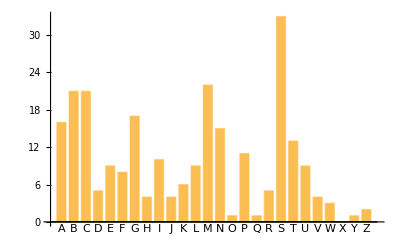

```mathematica
BarChart[Length[Cases[StringMatchQ[EntityValue[EntityList["Country"],"Name"],#~~___],True]]&/@ToUpperCase[Alphabet[]],ChartLabels->ToUpperCase[Alphabet[]]]
```

## 43. Storing Things

```mathematica
bin=CreateDatabin[];
```

```mathematica
DatabinAdd[bin,<|1->"test1",2->"test2"|>]
```

Databin[…]

```mathematica
Values[bin]
```

<|1→{test1},2→{test2}|>

```mathematica
Put[bin,LocalObject[]]
```

LocalObject[file:///home/ben/.Wolfram/Objects/c8eb30fd-0d37-45d3-bfd7-de8f50f1a2d7]

```mathematica
Values@Get[%]
```

{{<|1→test1,2→test2|>,Fri 23 Apr 2021 13:53:11GMT-4,data2e28106b-1f06-40bc-9700-703d648b8eb7,0.052 kB,<|TimeRecorded→Fri 23 Apr 2021 13:53:11GMT-4,TimeGiven→DateObject[Missing[]],Authenticated→False,GeoLocation→GeoPosition[{39.0526,-77.121}],SourceType→WolframLanguage,SourceDetails→<|UserAgent→Wolfram HTTPClient 12.2|>|>}}

## 44. Importing and Exporting

```mathematica
Take[<|#->LanguageIdentify[#]|>&/@TextSentences[Import["http://un.org"]],4]
```

{<|رسم توضيحي لفريق العمل المناخي التابع للأمم المتحدة→Arabic|>,<|联合国气候行动小组图片→Chinese|>,<|Illustration by the UN Climate Action Team→English|>,<|Illustration par l'Équipe de soutien sur les changements climatiques→French|>}

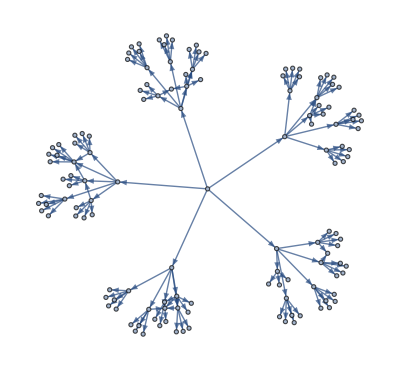

```mathematica
NestGraph[Take[Import[#,"Hyperlinks"],5]&,"http://wikipedia.org",3]
```

```mathematica
TextCases[Import["http://nato.int"],"Country"]
```

{Russia,Afghanistan,Ukraine,Czech Republic,Poland,Turkey,United States,Russia,Russian,German,Montenegro,US,Macedonia,Romania,US,US,Kosovo,Belgians,Ukraine,Russia,Ukraine,Ukraine,Russia,Ukraine,Russia,Ukraine,Norway,United Kingdom,US,S,U,S,Slovakia,US,US,Ukraine,US,Georgia,Russia,Afghanistan,Ukraine,Kosovo}

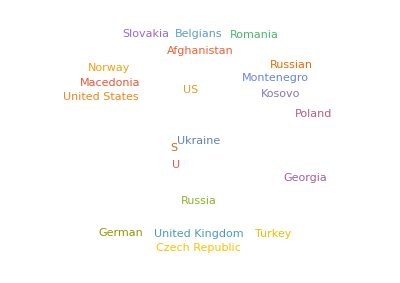

```mathematica
WordCloud[%]
```

## 45. Datasets

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

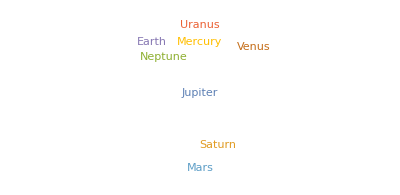

```mathematica
WordCloud[Normal[planets[All,"Mass"]]]
```

## 46. Writing Good Code

```mathematica
Module[{a,i},a=0;For[i=1,i≤1000,i++,a=i*(i+1)+a];a]
```

334334000

```mathematica
Fold[(#1+#2*(#2+1))&,0,Range[1000]]
```

334334000

```mathematica
ranges=Table[SortBy[Range[n],RandomReal[]&],{n,200}];
```

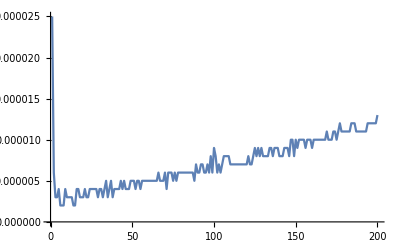

```mathematica
ListLinePlot[First[Timing[Sort[#]]]&/@ranges]
```

## 47. Debugging Your Code

```mathematica
Take[Counts[StringTake[#,2]&/@Select[WordList[],StringLength[#]≥2&]],10]
```

<|aa→2,ab→170,ac→217,ad→191,ae→26,af→72,ag→81,ah→5,ai→55,AI→1|>

```mathematica
Reap[Fold[10Sow[#1]+#2&,Range[5]]]//Last//Flatten
```

{1,12,123,1234}

```mathematica
Reap@Nest[If[EvenQ[#],Sow[#]/2,3#+1]&,1000,20]//Last//Flatten
```

{1000,500,250,376,188,94,142,214,322,484,242,364,182}